```mathematica
Series[Cos[x],{0,2}]
```

Series::sspec: Series specification {0,2} is not a list with three elements.

```mathematica
Series[Cos[x],{x,0,5}]
```

1-x^2/2+x^4/24+O[x]^6

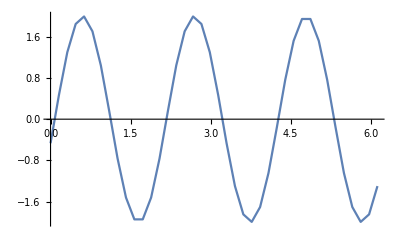

```mathematica
ListLinePlot[Partition[Flatten[Import["/home/andrey/CLionProjects/NumericalMethods/Lab10/files/U2.txt","Table"]],2],PlotRange->All]
```

```mathematica
Log[31/22,28/6.7]
```

4.17005

x-x^3/6+x^5/120-Sin[x]

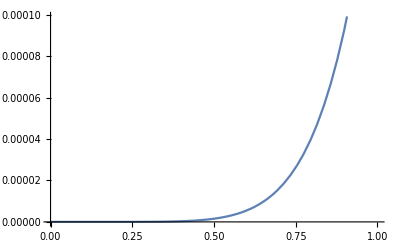

x-x^3/6+x^5/120+Sin[x]

```mathematica
delta[x_]=-Sin[x]+x -x^3/6 + x^5/120
Plot[delta[x],{x,0,1}]
```

```mathematica
normDeltaK = N[delta[1]]
```

0.000195682

0.5 (1+Sin[x])

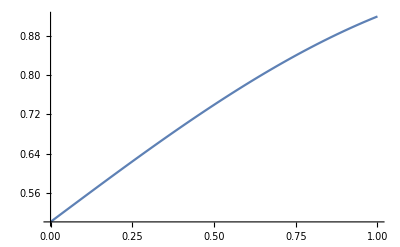

```mathematica
f[x_] = 0.5*(1+Sin[x])
Plot[f[x] ,{x,0,1}]
```

```mathematica
normF = N[f[1]]
```

0.920735

```mathematica
res=normDeltaK * 3 *3 *normF
```

0.00162154